# Solução empregando as funções de Airy para as tensões em uma chapa com furo sujeita a forças em x, y e z

-Graphics-

```mathematica
SigRR[ϕ_,r_,θ_]:=1/r D[ϕ,r]+1/r^2 D[ϕ,{θ,2}]
Sigθθ[ϕ_,r_,θ_]:=D[ϕ,{r,2}]
TauRθ[ϕ_,r_,θ_]:=1/r^2*D[ϕ,θ]-1/r*D[ϕ,r,θ]
(*
O Original era assim;
F3x=1/4*Sx(r^2-2a^2*Log[r]-((r^2-a^2)^2)/r^2 Cos [2(θ+Pi/2)]);
F3y=1/4*Sy(r^2-2a^2*Log[r]-((r^2-a^2)^2)/r^2 Cos [2θ]);
subst={pi->19.5,rw->0.10795,Sy->-45.9,Sx->-62.1,Sz->-48.2,ν->0.203};
*)


F3x=1/4*Sy(r^2-2a^2*Log[r]-((r^2-a^2)^2)/r^2 Cos [2(θ+Pi/2)]);
F3y=1/4*Sx(r^2-2a^2*Log[r]-((r^2-a^2)^2)/r^2 Cos [2θ]);
subst={pi->19.5,rw->4.25*0.0254,Sx->-45.9,Sy->-62.1,Sz->-48.2,e->29269.,nu->0.203}
solac={A->0,C->-a^2  (pi-po),a->rw,po->0};
F2 = A r^2 + C Log[r]/.solac;
ϕ=F3x+F3y+F2/.solac;
Print["Função de Airy para as devidas condições de contorno = ", ϕ]
SigR=SigRR[ϕ,r,θ];
SigT=Sigθθ[ϕ,r,θ];
TauRT=TauRθ[ϕ,r,θ];
SigZ=Sz+nu ((SigR+SigT)-(Sx+Sy))//Simplify;
stress={{SigR,TauRT,0},{TauRT,SigT,0},{0,0,SigZ}}/.{a->rw,po->0}//Simplify;
stress//MatrixForm
stress=stress/.subst;
myrule=Thread[{Cos[θ],Sin[θ],r,Cos[2θ]}->{x/Sqrt[x^2+y^2],y/Sqrt[x^2+y^2],Sqrt[x^2+y^2], (x^2-y^2)/(x^2+y^2)}];
RadialParaCartesiano[Sigmar_]:=
Block[{R,SigmaC},
R={{Cos[θ],Sin[θ],0},{-Sin[θ],Cos[θ],0},{0,0,1}};
SigmaC=Transpose[R].Sigmar.R;
SigmaC
];
stressR=stress;
stress=RadialParaCartesiano[stress];
SC=stress/.subst/.myrule//Simplify
(Vefificacao equilibrio)
Simplify[D[SigR,r]+(SigR-SigT)/r+1/r D[TauRT,θ]]
Simplify[(2TauRT)/r+D[TauRT,r]+1/r D[SigT,θ]]
Simplify[ϕ]
```

{pi→19.5,rw→0.10795,Sx→-45.9,Sy→-62.1,Sz→-48.2,e→29269.,nu→0.203}

Função de Airy para as devidas condições de contorno = -pi rw^2 Log[r]+1/4 Sx (r^2-((r^2-rw^2)^2 Cos[2 θ])/r^2-2 rw^2 Log[r])+1/4 Sy (r^2-((r^2-rw^2)^2 Cos[2 (π/2+θ)])/r^2-2 rw^2 Log[r])

((r^2 (-2 pi rw^2+(r^2-rw^2) (Sx+Sy))+(r^4-4 r^2 rw^2+3 rw^4) (Sx-Sy) Cos[2 θ])/(2 r^4) | -((r^4+2 r^2 rw^2-3 rw^4) (Sx-Sy) Cos[θ] Sin[θ])/r^4 | 0
-((r^4+2 r^2 rw^2-3 rw^4) (Sx-Sy) Cos[θ] Sin[θ])/r^4 | (r^2 (2 pi rw^2+(r^2+rw^2) (Sx+Sy))-(r^4+3 rw^4) (Sx-Sy) Cos[2 θ])/(2 r^4) | 0
0 | 0 | (r^2 Sz-2 nu rw^2 (Sx-Sy) Cos[2 θ])/r^2)

{{(-45.9 x^10+x^8 (0.0244717-229.5 y^2)+x^6 (0.00329987+1.18163 y^2-459. y^4)+y^6 (0.00329987-0.402035 y^2-45.9 y^4)+x^4 (-0.0164994 y^2+1.88782 y^4-459. y^6)+x^2 (-0.0164994 y^4+0.32862 y^6-229.5 y^8))/((x^2+y^2)^5),(0.+x^7 (0.0489435 y-1.42109×10^-14 y^3)+x^5 (0.0131995 y+1.65709 y^3)+x^3 (3.16734 y^5+1.42109×10^-14 y^7)+x (-0.0131995 y^5+1.5592 y^7))/((x^2+y^2)^5),0},{(0.+x^7 (0.0489435 y-1.42109×10^-14 y^3)+x^5 (0.0131995 y+1.65709 y^3)+x^3 (3.16734 y^5+1.42109×10^-14 y^7)+x (-0.0131995 y^5+1.5592 y^7))/((x^2+y^2)^5),(-62.1 x^10+x^8 (-0.402035-310.5 y^2)+x^6 (-0.00329987-1.93676 y^2-621. y^4)+y^6 (-0.00329987+0.779599 y^2-62.1 y^4)+x^4 (0.0164994 y^2-1.88782 y^4-621. y^6)+x^2 (0.0164994 y^4+0.426507 y^6-310.5 y^8))/((x^2+y^2)^5),0},{0.,0.,0.+(-48.2 x^4+0.0766454 y^2-48.2 y^4+x^2 (-0.0766454-96.4 y^2))/((x^2+y^2)^2)}}

equilibrio Vefificacao

0

0

(-(r^2-rw^2)^2 (Sx-Sy) Cos[2 θ]+r^2 (r^2 (Sx+Sy)-2 rw^2 (2 pi+Sx+Sy) Log[r]))/(4 r^2)

```mathematica
Simplify[ϕ]
```

(-(r^2-rw^2)^2 (Sx-Sy) Cos[2 θ]+r^2 (r^2 (Sx+Sy)-2 rw^2 (2 pi+Sx+Sy) Log[r]))/(4 r^2)

```mathematica
SigR=Simplify[SigRR[ϕ,r,θ]]
SigT=Simplify[Sigθθ[ϕ,r,θ]]
TauRT=Simplify[TauRθ[ϕ,r,θ]]
```

(r^2 (-2 pi rw^2+(r^2-rw^2) (Sx+Sy))+(r^4-4 r^2 rw^2+3 rw^4) (Sx-Sy) Cos[2 θ])/(2 r^4)

(r^2 (2 pi rw^2+(r^2+rw^2) (Sx+Sy))-(r^4+3 rw^4) (Sx-Sy) Cos[2 θ])/(2 r^4)

-((r^4+2 r^2 rw^2-3 rw^4) (Sx-Sy) Cos[θ] Sin[θ])/r^4

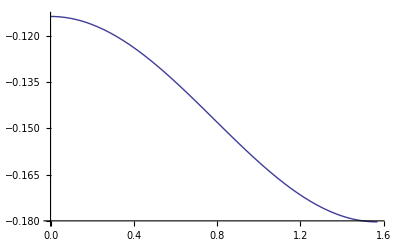

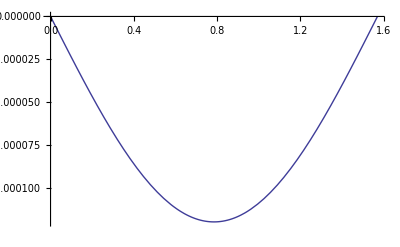

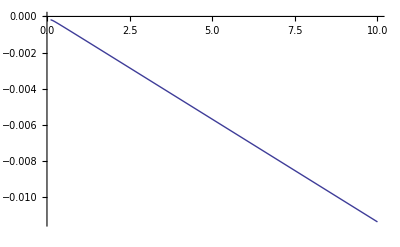

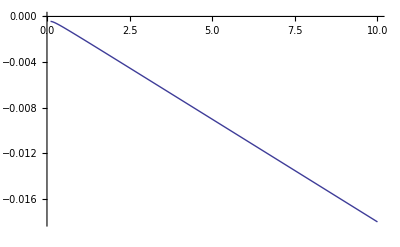

(0.+0. ⅈ)+(0.00882696+0. ⅈ) Cos[θ]+(0.026784+0. ⅈ) Sin[θ]

0.+0. ⅈ

```mathematica
Dmatrix=1/e{{1,-nu,0},{-nu,1.,0},{0,0,2(1+nu)}};
Dmatrix//MatrixForm;
sigvec={SigR,SigT,TauRT};
sigvec//MatrixForm;
Epsvec=Dmatrix.sigvec;
MatrixForm[Simplify[Epsvec]];
fd=0.;
ur=Simplify[Integrate[Epsvec[[1]],r]];
ut=Simplify[Integrate[Epsvec[[2]]r-ur,θ]];
(* verificar se D[ur,r] = Espvec[[1]], se a derivad de ur e ut sao iguais epsvec[[3]] *)
Plot[ur/.subst/.rw->4.25*0.0254/.r->100,{θ,0,Pi/2}]
Plot[ut/.subst/.rw->4.25*0.0254/.r->4.25*0.0254,{θ,0,Pi/2}]
Plot[ur/.subst/.rw->4.25*0.0254/.θ->0,{r,4.25*0.0254,10}]
Plot[ur/.subst/.rw->4.25*0.0254/.θ->Pi/2,{r,4.25*0.0254,10}]
fd=0.;
ux=ur Cos[θ]-ut Sin[θ];
uy=ur Sin[θ]+ut Cos[θ]/.subst;
fd=(ux Sx+uy Sy)/.rw->4.25*0.0254/.subst;
fd=Simplify[fd/.r->(1 4.25*0.0254)]
Integrate[fd,{θ,0,2Pi}]



(*Integrate[u,{θ,0,-Pi/2}]/.rw->4.25*0.0254*)
```

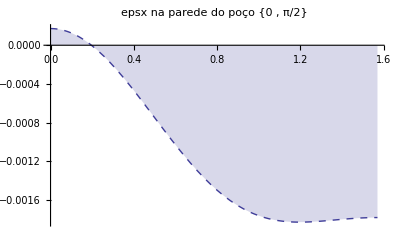

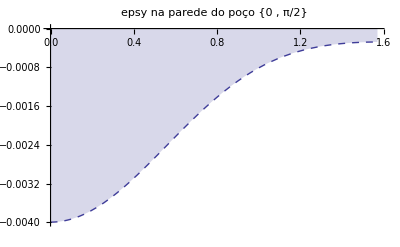

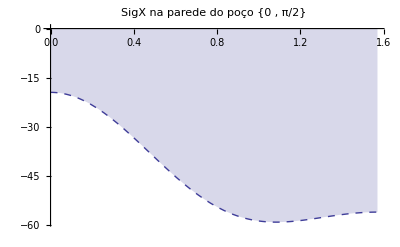

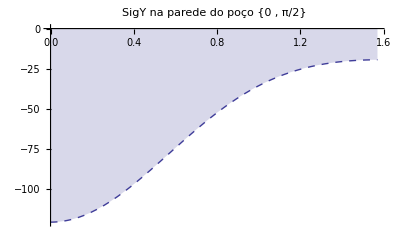

-19.5

-56.1

{-59.1681,{θ→1.0855}}

```mathematica
Dmatrix=1/e{{1,-nu,0},{-nu,1.,0},{0,0,2(1+nu)}};
Dmatrix//MatrixForm;
sigvec={SigR,SigT,TauRT};
sigvec//MatrixForm;
Epsvec=Dmatrix.sigvec/.subst;
eps={{Epsvec[[1]],Epsvec[[3]],0},{Epsvec[[3]],Epsvec[[2]],0},{0,0,0}};
eps=RadialParaCartesiano[eps];
Plot[{eps[[1,1]]}/.r->4.25*0.0254,{θ,0,Pi/2},AxesOrigin->{0,0},Filling->Axis,PlotStyle->{Thick,Dashed},PlotRange->All,PlotLabel->" epsx na parede do poço {0 , π/2} "]
Plot[eps[[2,2]]/.r->4.25*0.0254,{θ,0,Pi/2},AxesOrigin->{0,0},Filling->Axis,PlotStyle->{Thick,Dashed},PlotRange->All,PlotLabel->" epsy na parede do poço {0 , π/2} "]
Plot[stress[[1,1]]/.r->4.25*0.0254/.subst,{θ,0,Pi/2},AxesOrigin->{0,0},Filling->Axis,PlotStyle->{Thick,Dashed},PlotRange->All,PlotLabel->" SigX na parede do poço {0 , π/2} "]
Plot[stress[[2,2]]/.r->4.25*0.0254/.subst,{θ,0,Pi/2},AxesOrigin->{0,0},Filling->Axis,PlotStyle->{Thick,Dashed},PlotRange->All,PlotLabel->" SigY na parede do poço {0 , π/2} "]
stress[[1,1]]/.r->4.25*0.0254/.subst/.θ->0
stress[[1,1]]/.r->4.25*0.0254/.subst/.θ->Pi/2
FindMinimum[stress[[1,1]]/.r->4.25*0.0254/.subst,{θ,0.5}]
```

```mathematica
stress[[1,2]]
```

Cos[θ] (-(16.2 (-0.000407391+0.0233064 r^2+r^4) Cos[θ]^2 Sin[θ])/r^4-((r^2 (0.454475-108. (0.0116532+r^2))-16.2 (0.000407391+r^4) Cos[2 θ]) Sin[θ])/(2 r^4))+Sin[θ] ((Cos[θ] (r^2 (-0.454475-108. (-0.0116532+r^2))+16.2 (0.000407391-0.0466128 r^2+r^4) Cos[2 θ]))/(2 r^4)+(16.2 (-0.000407391+0.0233064 r^2+r^4) Cos[θ] Sin[θ]^2)/r^4)

```mathematica
t={{10,2,3},{4,19,2},{17,21,13}}
Eigenvalues[t]//N
```

{{10,2,3},{4,19,2},{17,21,13}}

{25.9903,11.7697,4.23996}

-90.

{A→152.54,B→0.0015489,C→146.29}

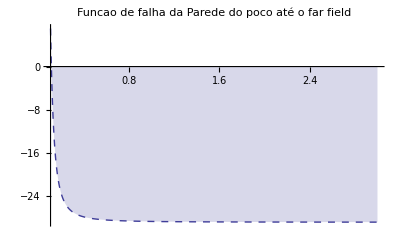

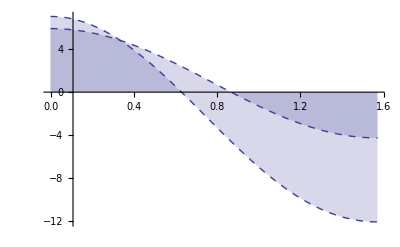

36.0593

```mathematica
s[sigma_]:=sigma-(1/3 Tr[sigma] IdentityMatrix[Length[sigma]]);
j2[sigma_]:=1/2 Tr[s[sigma].s[sigma]];
Plot[SC[[1,1]]/.{y->0},{x,0.10795,3},AxesOrigin->{0.10795,0},Filling->Axis,PlotStyle->{Thick,Dashed},PlotRange->All];
Plot[stress[[1,1]]/.{θ->0},{r,0.10795,3},AxesOrigin->{0.10795,0},Filling->Axis,PlotStyle->{Thick,Dashed},PlotRange->All];
Plot[{stress[[2,2]]}/.{r->0.10795},{θ,0,Pi/2},AxesOrigin->{0.10795,0},Filling->Axis,PlotStyle->{Thick,Dashed}];
d=D[stress[[2,2]]/.{r->0.10795},θ];
principal=Eigenvalues[stress];
(*Solve[d==0,θ]*)
Plot[d,{θ,0,Pi/2}];
FindRoot[d,{θ,0.5}][[1,2]]180/Pi
I1=Tr[stress];
sub={A->152.54,B->0.0015489,C->146.29}
S=s[stress];
SqJ2=Sqrt[j2[stress]];
FF=SqJ2-(A-C Exp[B I1])/.sub;
(*sigma[0]-sigma[2]+(sigma[0]+sigma[2])*sinphi-2.*c*cosphi;*)
sig11=principal[[3]];
sig33=principal[[1]];
phi=0.2265;
coesao=6.5;
FMohr=(sig11-sig33)+(sig11+sig33)Sin[phi]-2coesao Cos[phi];
Plot[FF/.{θ->0},{r,0.10795,3},AxesOrigin->{0.10795,0},Filling->Axis,PlotStyle->{Thick,Dashed},PlotRange->All,PlotLabel->"Funcao de falha da Parede do poco até o far field "]
Plot[{FMohr,FF}/.{r->0.10795},{θ,0,Pi/2},AxesOrigin->{0.10795,0},Filling->Axis,PlotStyle->{Thick,Dashed},PlotRange->All]
FindRoot[(FF/.{r->0.10795}),{θ,0.9}][[1,2]]180/Pi
```

```mathematica
Cos[0.22](79-47.8)/2
```

15.224

```mathematica
Sqrt[400.]
```

20.

```mathematica
Sqrt[539.]
Sqrt[182.]
```

23.2164

13.4907

```mathematica
sigmax=-47.8;
sigmin=-78.2;
(Sin[0.2265](sigmax+sigmin)+(sigmax-sigmin))/(2Cos[0.2265])
```

1.07978